The Wolfram quantum framework integrates with standard computational analysis and modeling tools, enabling symbolic quantum computations, numerical measurement-based quantum computing, and interaction with quantum hardware. A recent addition to the framework is the Suzuki-Trotter decomposition, known as Trotterization, which simulates quantum time evolution in circuits. This computational essay briefly reviews Trotterization within the framework and demonstrates its application through examples, showcasing its utility in modeling quantum systems.

## Paclet installation

Install quantum paclet (to add quantum functions to WL):

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

```mathematica
Names["*Quantum*"]
```

{QuantumBasis,QuantumChannel,QuantumCircuitMultiwayCausalGraph,QuantumCircuitMultiwayGraph,QuantumCircuitOperator,QuantumDistance,QuantumEntangledQ,QuantumEntanglementMonotone,QuantumEvolve,QuantumMeasurement,QuantumMeasurementOperator,QuantumMeasurementSimulation,QuantumMPO,QuantumMPS,QuantumOperator,QuantumPartialTrace,QuantumPartialTranspose,QuantumShortcut,QuantumState,QuantumStateEstimate,QuantumStateEstimation,QuantumStateSampler,QuantumTensorProduct,QuantumWeylTransform,QuantumWignerTransform}

## Time evolution and Trotterization

Consider a simple Ising-type of Hamiltonian for three qubits as H=X_1+X_2+X_3-Z_1 Z_2-Z_2 Z_3 with X/Z Pauli operators:

```mathematica
h=QuantumOperator["X"+("X"->{2})+("X"->{3})-"ZZ"-("ZZ"->{2,3})];
```

The decomposition into Pauli matrices:

```mathematica
h["PauliDecompose"]
```

<|XII→1,ZZI→-1,IXI→1,IZZ→-1,IIX→1|>

Also, the Hamiltonian can be constructed differently:

```mathematica
h==Sum[QuantumOperator["X",{i}],{i,3}]-Total[QuantumOperator["ZZ",#]&/@Partition[Range[3],2,1]]
```

True

Find time-dependent state:

```mathematica
ψt=QuantumEvolve[h,{t,0,10}];
```

Plot bit-string probabilities in time:

```mathematica
ListAnimate[BarChart[#,ChartLabels->StringJoin@@@Tuples[{"0","1"},3],PlotRange->{-.1,1}]&/@Table[ψt["Probabilities"],{t,0,10,.1}]]
```

Now let’s explore how a circuit can mimic the above time evolution. The goal is to create a quantum circuit, approximating the time evolution operator. For the simple case of time-independent Hamiltonian, it means a circuit mimicking Exp[-ⅈ t H], to some approximation. Assuming H=∑_i A_i, the exponential product formula (ie the Suzuki-Trotter decomposition) will be very useful.

Trotterization can be implemented in our framework as follows: QuantumCircuitOperator[{"Trotterization", ListOfOperators, OrderOfApproximation, NumerOfSteps, OverallTime}]
where ListOfOperators are in fact the list of operators constructing the Hamiltonian, and OrderOfApproximation represents the order corrections to the exponential product formula.

List of Pauli operators where h=Total[ops] (note it is useful to do so because here the operator h depends only on Pauli operators)

```mathematica
ops=KeyValueMap[QuantumOperator[#2 #1]&,h["PauliDecompose"]];
```

Trotter-Suzuki decomposition of first order and one step:

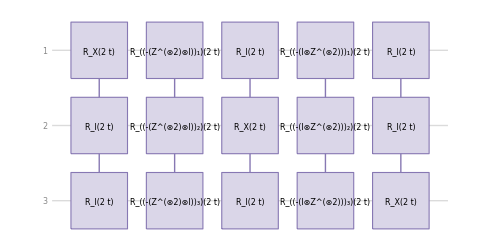

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,1,1,t}]["Diagram",FontSize->8]
```

Trotter-Suzuki decomposition of first order and two steps:

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,1,2,t}]["Diagram",FontSize->8]
```

-Graphics-

Trotter-Suzuki decomposition of 2nd order and one step:

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,2,1,t}]["Diagram"]
```

-Graphics-

Trotter-Suzuki decomposition of 2nd order and two steps:

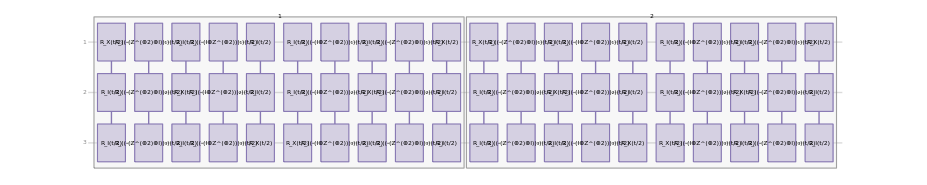

```mathematica
QuantumCircuitOperator[{"Trotterization",ops,2,2,t}]["Diagram",FontSize->6]
```

Calculate the trace distance between the evolution operator at time t=1 with the one obtained from the Troterrization (to do so, I will use QuantumDistance, but we should wrap the operator matrices as QuantumState, first, to feed it into QuantumDistance) :

```mathematica
u=MatrixExp[-ⅈ h["Matrix"]];//AbsoluteTiming
```

{16.1191,Null}

```mathematica
uf=QuantumState[u];
```

```mathematica
tracDis=Table[With[{c=N[QuantumCircuitOperator[{"Trotterization",N@ops,order,steps,1}]]},{c["Gates"],QuantumDistance[QuantumState[c["Matrix"]],uf,"Trace"]}],{order,{1,2,4}},{steps,1,10}];//AbsoluteTiming
```

{300.097,Null}

Visualize it:

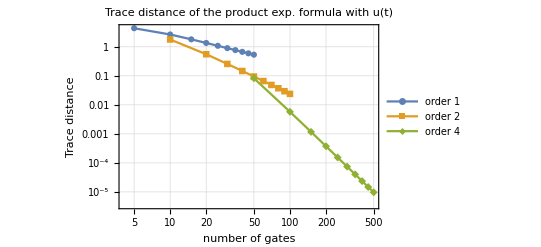

```mathematica
ListLogLogPlot[tracDis,]
```

Another metric one can use to test how good the Trotterization approximate the actual evolution operator is the spectral norm (which is Norm[...,2] in Wolfram Language).

```mathematica
norm2=Table[With[{c=N[QuantumCircuitOperator[{"Trotterization",N@ops,order,steps,1}]]},{c["Gates"],Norm[c["Matrix"]-u,2]}],{order,{1,2,4}},{steps,1,10}];//AbsoluteTiming
```

{94.8885,Null}

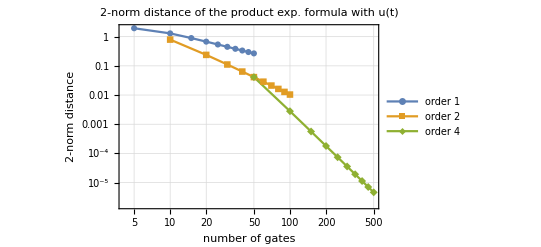

```mathematica
ListLogLogPlot[norm2,]
```

Note that the 2-norm distance is the same as the ideal error (ϵ=||u(t)-Trotterized||/||u(t)||) since ||u(t)||=1.

## CITE THIS NOTEBOOK

Suziki-Trotter decomposition: simulating Hamiltonian dynamics
by Mads Bahrami
Wolfram Community, STAFF PICKS, NOV 7, 2022
https://community.wolfram.com/groups/-/m/t/2687830